## Alpha-Spektroskopie

### Imports

```mathematica
Filenames = {"AIR", "AMSPKTR","CALIBR"};
Filepaths=NotebookDirectory[]<>"..\\data\\"<>#1&/@Filenames;

rawData = Import[#1<>".DAT","List"] &/@Filepaths ;
kalibrData = rawData[[3]];
airData=rawData[[1]];
sptrData=rawData[[2]];
```

### Energie-Kalibration

{ | Estimate | Standard Error | t-Statistic | P-Value
μ | 33.6787 | 0.128487 | 262.118 | 8.97527254663×10^-939
σ | 1.30333 | 0.128489 | 10.1435 | 4.22007×10^-23
k | 22906.6 | 1955.69 | 11.7128 | 8.04371×10^-30, | Estimate | Standard Error | t-Statistic | P-Value
μ | 138.253 | 0.113263 | 1220.64 | 8.88241422653×10^-1618
σ | 1.27434 | 0.113263 | 11.2512 | 9.10901×10^-28
k | 24651.9 | 1897.51 | 12.9917 | 7.94103×10^-36, | Estimate | Standard Error | t-Statistic | P-Value
μ | 452.902 | 0.129501 | 3497.3 | 2.16471935097×10^-2084
σ | 1.26956 | 0.129494 | 9.80396 | 9.5217×10^-22
k | 21971.7 | 1940.92 | 11.3203 | 4.528×10^-28, | Estimate | Standard Error | t-Statistic | P-Value
μ | 968.743 | 0.0495681 | 19543.7 | 2.43448612328×10^-2847
σ | 1.06534 | 0.0495747 | 21.4897 | 8.29052×10^-85
k | 34850.7 | 1404.34 | 24.8164 | 9.21397×10^-107}

{7011.605764712136/E^(0.29434965581444056*(-33.67872074878762 + x)^2),7717.455825318301/E^(0.30789071693589276*(-138.25335222258695 + x)^2),6904.329823546912/E^(0.31021660410784563*(-452.90210260199433 + x)^2),13050.635733856781/E^(0.4405445287921415*(-968.7432082800937 + x)^2)}

357.4458819940879 + 5.294028183565216*x

{357.4458819940879 + 5.294028183565216*x - 4.302652729749464*Sqrt[129.33390238062464 - 0.26700597705105833*x + 0.00013781903972842876*x^2], 357.4458819940879 + 5.294028183565216*x + 4.302652729749464*Sqrt[129.33390238062464 - 0.26700597705105833*x + 0.00013781903972842876*x^2]}

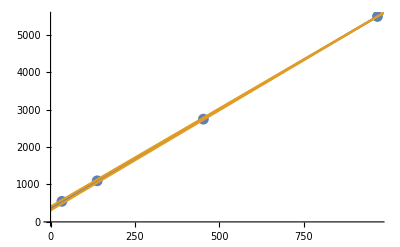

```mathematica
kalibrDampening={10,5,2,1};
kalibrPeakPositions={34,138,452,968};
model[x_] =k*Exp[-1/2 ((x-μ)/σ)^2]/(σ √(2 π));

kalibrFits=NonlinearModelFit[kalibrData, model[x], {{μ, #1}, {σ, 2}, {k, 8000}}, x]&/@kalibrPeakPositions;


kalibrParameters=#1[[1,1]]&/@(#1[[{1,2}]]&/@#1["ParameterTableEntries"]&/@kalibrFits);

kalibrParameters=MapThread[{#1,#2}&,{kalibrParameters,5486/#1&/@kalibrDampening}];
kalibrParametersLatex=MapThread[Join[#1,{Max[(#1[[2]])/20*(#2-1),1]}]&,{kalibrParameters,kalibrDampening}];
errors=kalibrParametersLatex[[All,3]];
kalibrFunction=NonlinearModelFit[kalibrParameters,a x+b,{a,b},{x},Weights->1/errors^2];

kalibrFitFunctions=Normal/@kalibrFits;

bands95[x_]= nlm["SinglePredictionBands",ConfidenceLevel->0.95];
Export[Filepaths[[3]] <>"-fitted.DAT", N[kalibrParametersLatex], "Table"];



#1["ParameterTable"]&/@kalibrFits
Format[#1,InputForm]&/@kalibrFitFunctions

Format[Normal[kalibrFunction],InputForm]
Format[bands95[x],InputForm]
Show[ListPlot[kalibrParameters],Plot[{Normal[kalibrFunction],bands95[x]},{x,0,1000}]]
```

### Alpha-Peaks von Amerikanum

{ | Estimate | Standard Error | t-Statistic | P-Value
μ | 5.39195 | 0.000499372 | 10797.5 | 4.41432×10^-16
σ | 0.0134627 | 0.000630047 | 21.3678 | 0.000028366
k | 17.361 | 0.645508 | 26.8951 | 0.0000113623, | Estimate | Standard Error | t-Statistic | P-Value
μ | 5.44773 | 0.000379607 | 14351. | 3.11814×10^-20
σ | 0.0129335 | 0.000393809 | 32.8421 | 4.91863×10^-7
k | 126.18 | 3.30838 | 38.1394 | 2.33474×10^-7, | Estimate | Standard Error | t-Statistic | P-Value
μ | 5.48574 | 0.00016942 | 32379.6 | 9.26931×10^-34
σ | 0.0102191 | 0.000173238 | 58.9885 | 7.57687×10^-12
k | 592.271 | 8.568 | 69.1259 | 2.13539×10^-12, | Estimate | Standard Error | t-Statistic | P-Value
μ | 5.53225 | 0.000719869 | 7685.08 | 1.72011×10^-15
σ | 0.0123526 | 0.000582254 | 21.2152 | 0.0000291849
k | 5.57282 | 0.278861 | 19.9842 | 0.0000369988}

{5.29148,5.57206}

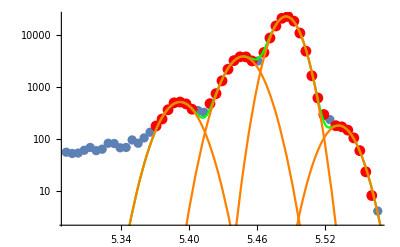

```mathematica
offset=8;
relevantSptrData=Take[MapIndexed[{(Normal[kalibrFunction]/.x->First[#2])/1000,#1}&,sptrData],{940-offset,985}];
model[x_] =k*Exp[-1/2 ((x-μ)/σ)^2]/(σ √(2 π));
model2[x_] =a*Exp[b*x]+c;
intervals={{8,14},{17,24},{26,36},{38,44}} + offset;

linearInterval={3,7};
spktrDataIntervals = Take[relevantSptrData,{#1[[1]],#1[[2]]}]&/@intervals;

spktrPeakFits=NonlinearModelFit[#1, model[x], {{μ, Mean[#1[[All,1]]]}, {σ, 1.86}, {k,Mean[#1[[All,2]]]}}, x]&/@spktrDataIntervals;
#1["ParameterTable"]&/@spktrPeakFits
spktrPeakFits=spktrPeakFits//Normal;

{First[relevantSptrData][[1]],Last[relevantSptrData][[1]]}

Export[Filepaths[[2]] <>"-calibrated.DAT", N[relevantSptrData], "Table"];

Show[
ListLogPlot[relevantSptrData,PlotRange->All],
ListLogPlot[Flatten[spktrDataIntervals,1],PlotStyle->Red],
LogPlot[Total[spktrPeakFits],{x,First[relevantSptrData][[1]],Last[relevantSptrData][[1]]},PlotStyle->Green],
LogPlot[spktrPeakFits,{x,First[relevantSptrData][[1]],Last[relevantSptrData][[1]]},PlotStyle->Orange]
]
```